## Governing Equations

Conservation of mass

```mathematica
mass conservation = 1/r^2 Dt[ρ u r^2,r]==q;
```

Conservation of momentum

```mathematica
momentum conservation =ρ u Dt[u,r]+Dt[p,r]==-q u -GM/r^2 ρ;
```

Conservation of energy

```mathematica
energy conservation=(1/r^2 Dt[r^2 ρ u(1/2 u^2+(γ p/ρ)/(γ-1)),r]==1/2 q vw^2-GM/r^2 ρ u/.Dt[γ,_]:>0);
```

Mass source term

```mathematica
mass source=DD r^-η;
```

## Reduction to Dimensionless variable

Bondi radius

```mathematica
bondi radius=GM/vw^2;
```

Bondi density

```mathematica
DD*(bondi radius)^-η*(bondi radius/vw);
PowerExpand[%];
bondi density=%;
```

Mass conservation

```mathematica
{mass conservation,momentum conservation,energy conservation};
% /. q-> mass source;
% /. HoldPattern[Dt[z_,r]]->  Dt[z,ξ]/Dt[r,ξ];
% /. p-> bondi density*vw^2*p;
% /. ρ-> bondi density ρ;
% /. u-> vw u;
% /. r-> bondi radius*ξ;
% /. Dt[η,_]:>0;
% /. Dt[DD,_]:>0;
% /. Dt[vw,_]:>0;
% /. Dt[GM,_]:>0;
% /. Dt[γ,_]:>0;
Simplify[%];
Solve[%,{Dt[ρ,ξ],Dt[u,ξ],Dt[p,ξ]}][[1]];
PowerExpand[%];
Simplify[%];
dimles derivs=%;
```

## Integral expressions

Mass conservation

```mathematica
mass source;
%*r^2;
Integrate[%,r];
%-(%/.r->rs);
ρ u r^2==%;
integral mass conservation=%
```

r^2 u ρ==(DD r^(3-η))/(3-η)-(DD rs^(3-η))/(3-η)

Validation

```mathematica
integral mass conservation;
Dt[%,r];
% /. Solve[mass conservation,Dt[ρ,_]][[1]];
% /. q-> mass source;
% /. Dt[DD,_]:>0;
% /. Dt[η,_]:>0;
% /. Dt[rs,_]:>0;
Simplify[%]
```

True

Energy conservation

```mathematica
-(GM u ρ)/r^2;
% /. Solve[integral mass conservation,ρ][[1]];
%*r^2;
Integrate[%,r];
%-(%/.r->rs);
%/integral mass conservation[[2]];
Simplify[%];
1/2 u^2-1/2 vw^2+c^2/(γ-1)==%;
integral energy conservation=%
```

u^2/2-vw^2/2+c^2/(-1+γ)==(GM (r^3 rs^η+r^(1+η) rs^2 (-3+η)-r^η rs^3 (-2+η)))/(r (-r^η rs^3+r^3 rs^η) (-2+η))

Validation

```mathematica
integral energy conservation;
%[[1]]*integral mass conservation[[2]]==%[[2]]*integral mass conservation[[2]];
% /. c-> √(γ p/ρ);
Dt[%,r];
% /. Solve[{mass conservation,
momentum conservation,
energy conservation},{Dt[p,r],Dt[ρ,r],Dt[u,r]}][[1]];
% /. q-> mass source;
% /. Dt[γ,_]:>0;
% /. Dt[rs,_]:>0;
% /. Dt[GM,_]:>0;
% /. Dt[vw,_]:>0;
% /. Dt[η,_]:>0;
% /. Dt[DD,_]:>0;
%/.p-> ρ c^2/γ;
% /. Solve[integral mass conservation,ρ][[1]];
Simplify[%]
```

True

## Solutions without gravity

```mathematica
{mass conservation,momentum conservation,energy conservation};
% /. q-> mass source;
%/. p-> ρ c^2/γ;
% /. Dt[u,r]->0;
% /. Dt[c,r]->0;
% /. ρ->A r^(1-η);
% /. GM->0;
% /. Dt[γ,_]:>0;
% /. Dt[A,_]:>0;
% /. Dt[α,_]:>0;
% /. Dt[η,_]:>0;
Simplify[%];
Solve[%,{A,u,c}][[3]];
asymptotic prefactors=%
```

{A→(-(5 ⅈ DD √(-1+γ) √(-1+η))/(√(-1-5 γ+η+γ η))+(6 ⅈ DD √(-1+γ) √(-1+η))/((1-γ) √(-1-5 γ+η+γ η))+(ⅈ DD √(-1+γ) √(-1+η) η)/(√(-1-5 γ+η+γ η))-(2 ⅈ DD √(-1+γ) √(-1+η) η)/((1-γ) √(-1-5 γ+η+γ η)))/(3 vw-4 vw η+vw η^2),u→(ⅈ vw √(-1+γ) √(-1+η))/(√(-1-5 γ+η+γ η)),c→(√(-vw^2+vw^2 γ+vw^2/(1+5 γ-η-γ η)-(2 vw^2 γ)/(1+5 γ-η-γ η)+(vw^2 γ^2)/(1+5 γ-η-γ η)-(vw^2 η)/(1+5 γ-η-γ η)+(2 vw^2 γ η)/(1+5 γ-η-γ η)-(vw^2 γ^2 η)/(1+5 γ-η-γ η)))/(√2)}

```mathematica
u/c/.asymptotic prefactors;
asymptotic mach number=Simplify[%,vw>0]
```

(ⅈ √(-1+γ) √(-1+η))/(√(((-1+γ) γ (-3+η))/(-1+γ (-5+η)+η)) √(-1+γ (-5+η)+η))

Condition for supersonic flow at large distances

```mathematica
asymptotic mach number==1;
Solve[%,η][[1]]
```

{η→(1+3 γ)/(1+γ)}

## Freefall solution

In this case we consider the opposite extereme case, e.g. very close to the gravitating mass.

```mathematica
integral energy conservation;
%[[2]];
% /. r-> x rs;
PowerExpand[%];
Simplify[%];
% /. x^3-x^η-> -x^η;
%*x;
Expand[%];
% /. x->0;
Simplify[%,η<3];
%/(r/rs);
freefall energy conservation=1/2 u^2+c^2/(γ-1)==%
```

u^2/2+c^2/(-1+γ)==GM/r

```mathematica
integral mass conservation;
% /. r^(3-η)->0;
ρ/.Solve[%,ρ][[1]];
freefall density=%
```

(DD rs^(3-η))/(r^2 u (-3+η))

```mathematica
momentum conservation;
% /. p-> ρ c^2/γ;
% /. ρ-> freefall density;
% /. q->0;
% /. Solve[freefall energy conservation,c][[2]];
% /. Dt[η,_]:>0;
% /. Dt[γ,_]:>0;
% /. Dt[rs,_]:>0;
% /. Dt[DD,_]:>0;
% /. Dt[GM,_]:>0;
Simplify[%,DD>0];
% /. u-> A/√r;
% /. Dt[A,_]:>0;
A/(√r)/.Solve[%,A][[1]];
freefall velocity=%
```

-(√2 √GM)/(√r)

This is true unless γ == 5/3

## Secular Analytic solution

```mathematica
A/.asymptotic prefactors;
% /. γ->5/3;
%/.η->5/2;
%/r^(3/2);
Simplify[%];
secular density=%
```

(4 √(2/3) DD)/(r^(3/2) vw)

```mathematica
mass conservation;
% /. ρ-> secular density;
% /. q-> mass source;
% /. η->5/2;
% /. Dt[DD,_]:>0;
% /. Dt[vw,_]:>0;
%/.u-> u[r];
u[r]/.DSolve[%,u[r],r][[1]];
% /. C[1]->-√GM;
secular velocity=%
```

-(√GM)/(√r)+1/2 √(3/2) vw

```mathematica
r/.Solve[secular velocity==0,r][[1]];
secular stagnation=%
```

(8 GM)/(3 vw^2)

```mathematica
integral energy conservation;
% /. u-> secular velocity;
% /. c->√c2;
% /. rs-> secular stagnation;
c2/.Solve[%,c2][[1]];
% /. η->5/2;
% /. γ->5/3;
ExpandAll[%];
PowerExpand[%];
Simplify[%];
secular c2=%
```

GM/(3 r)+(5 vw^2)/24

Validation

```mathematica
{mass conservation,momentum conservation,energy conservation};
%/.p-> ρ c^2/γ;
% /. u-> secular velocity;
% /. ρ->secular density;
% /. c->√(secular c2);
% /. q-> mass source;
% /. η->5/2;
% /. γ->5/3;
% /. Dt[vw,_]:>0;
% /. Dt[DD,_]:>0;
% /. Dt[GM,_]:>0;
% /. Dt[γ,_]:>0;
Simplify[%]
```

{True,True,True}

## Mach number equation

```mathematica
{momentum conservation,integral energy conservation,integral mass conservation};
% /.q-> mass source;
% /. p-> ρ c^2/γ;
%/. u-> m c;
%/.Solve[%[[3]],ρ][[1]];
%/.Solve[%[[2]],c][[1]];
% /. Dt[γ,_]:>0;
% /. Dt[DD,_]:>0;
% /. Dt[η,_]:>0;
% /. Dt[rs,_]:>0;
% /. Dt[GM,_]:>0;
% /. Dt[vw,_]:>0;
%[[1]];
Simplify[%,γ>1];
raw mach number equation=%;
```

```mathematica
raw mach number equation;
% /. Dt[m,r]-> Dt[m,ξ]/Dt[r,ξ];
% /. r-> ξ bondi radius;
% /. rs-> ξs bondi radius;
% /. Dt[GM,_]:>0;
% /. Dt[vw,_]:>0;
Simplify[%];
Dt[m,ξ]/.Solve[%,Dt[m,ξ]][[1]];
PowerExpand[%];
Simplify[%];
mach number derivative=%
```

(m (2+m^2 (-1+γ)) (2 (-1+γ) ξ^(1+2 η) (6+η (-2+ξs)-2 ξs) ξs^5+(-5+3 γ) (-2+η) ξ^(2 η) ξs^6+(1+γ (3-m^2 (-3+η))+m^2 γ^2 (-3+η)-2 η) ξ^6 ξs^(2 η)+(-1+γ) (-2+η) (-1+m^2 γ (-3+η)+η) ξ^7 ξs^(2 η)-(-1+γ) (1+m^2 γ (-3+η)+η) ξ^(4+η) (3+η (-1+ξs)-2 ξs) ξs^(2+η)+(-2+η+η^2-m^2 γ^2 (6-5 η+η^2)+γ (-6+3 η-η^2+m^2 (6-5 η+η^2))) ξ^(3+η) ξs^(3+η)))/(2 (-1+m^2) (-1+γ) ξ (-ξ^η ξs^3+ξ^3 ξs^η) (-ξ^(1+η) (6+η (-2+ξs)-2 ξs) ξs^2-2 (-2+η) ξ^η ξs^3+2 ξ^3 ξs^η+(-2+η) ξ^4 ξs^η))

```mathematica
mach number derivative;
% /. {γ->4/3,η->226/100};
Simplify[%];
Numerator[%];
%/m;
% /. m^2->1;
%/.ξs->4;
Solve[%==0,ξ]
```

$Aborted

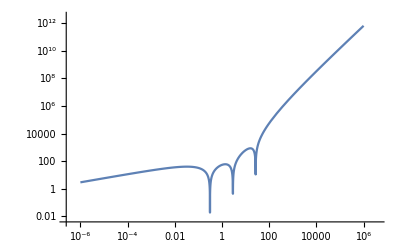

```mathematica
Numerator[mach number derivative];
% /. m->1;
%/(γ+1);
Expand[%];
Simplify[%];
Collect[%,ξ];
% /. η->2.7;
% /.γ->5./3.;
%/.ξs->2.9;
Simplify[%];
%/ξ^Limit[ξ D[Log[%], ξ],ξ->0];
Simplify[%];
LogLogPlot[Abs[%],{ξ,10^-6,10^6}]
```

```mathematica
shoot outside in[γval_,ηval_,ξsval_]:=Module[{ξsonic eqn,ξso,ξsi,ξ inner low,ξ inner high,ξ outer low,ξ outer high,sol inner,
sol outer,mder,m inner low, m outer high},
ξsonic eqn= Numerator[mach number derivative];
ξsonic eqn=ξsonic eqn/ξ^η;
ξsonic eqn=ξsonic eqn/.{η->ηval,ξs->ξsval,γ->γval,m->-1};
ξsonic eqn=Simplify[ξsonic eqn/ξ^Limit[ξ D[Log[ξsonic eqn], ξ],ξ->0]];
ξsonic eqn=ExpandAll[ξsonic eqn];
ξso=ξ/.FindRoot[ξsonic eqn,{ξ,1.01*ξsval,10^3 ξsval}][[1]];
ξsi=ξ/.FindRoot[ξsonic eqn,{ξ,10^-3*ξsval,0.99*ξsval}][[1]];
ξ inner low=ξsi*(1+10^-6);
ξ inner high=ξsval*(1-10^-6);
ξ outer low = ξsval*(1+10^-6);
ξ outer high=ξso*(1-10^-6);
m inner low=-1*(ξ inner low-ξsval)/(ξsi-ξsval);
m outer high=1*(ξ outer high-ξsval)/(ξso-ξsval);
mder = mach number derivative;
mder = mder/.{η->ηval,ξs->ξsval,γ->γval};
mder = mder/.m->m[ξ];
sol inner = NDSolve[{m'[ξ]==mder,m[ξ inner low]==m inner low},m[ξ],{ξ,ξ inner low,ξ inner high}][[1]];
sol outer = NDSolve[{m'[ξ]==mder,m[ξ outer high]==m outer high},m[ξ],{ξ,ξ outer low,ξ outer high}][[1]];
(D[(m[ξ]/.sol inner), ξ]/.ξ-> ξ inner high)-(D[(m[ξ]/.sol outer), ξ]/.ξ-> ξ outer low)
]
shoot outside in[5./3.,2.7,5]
```

-0.178741

```mathematica
{ξs/.FindRoot[shoot outside in[5./3.,2.5,ξs]==0,{ξs,2,6},Evaluated->False],8./3}
```

{2.66667,2.66667}

```mathematica
Table[ξs/.FindRoot[shoot outside in[4./3.,ηval,ξs]==0,{ξs,1,10},Evaluated->False],{ηval,2.4,2.9,0.1}]
```

{4.91833,4.72104,4.54005,4.37337,4.21929,4.07642}

```mathematica
Table[ξs/.FindRoot[shoot outside in[5./3.,ηval,ξs]==0,{ξs,1,10},Evaluated->False],{ηval,2.4,2.9,0.1}]
```

{2.77143,2.66667,2.57004,2.48066,2.39776,2.3207}

```mathematica
Table[ξs/.FindRoot[shoot outside in[γval,ηval,ξs]==0,{ξs,2,6},Evaluated->False],{γval,4./3.,5./3.,0.1},{ηval,2.4,2.9,0.1}]
```

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

{{4.91833,4.72104,4.54005,4.37337,4.21929,4.07642},{3.94115,3.78498,3.64159,3.50942,3.38718,3.27378},{3.32244,3.19286,3.07371,2.96377,2.86202,2.76756},{2.8897,2.77941,2.67779,2.58388,2.49683,2.41595}}

```mathematica
data= Table[{γval,ηval,ξs/.FindRoot[shoot outside in[γval,ηval,ξs]==0,{ξs,2,6},Evaluated->False]},{γval,4./3.,5./3.,0.1},{ηval,2.4,2.9,0.1}]
```

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

{{{1.33333,2.4,4.91833},{1.33333,2.5,4.72104},{1.33333,2.6,4.54005},{1.33333,2.7,4.37337},{1.33333,2.8,4.21929},{1.33333,2.9,4.07642}},{{1.43333,2.4,3.94115},{1.43333,2.5,3.78498},{1.43333,2.6,3.64159},{1.43333,2.7,3.50942},{1.43333,2.8,3.38718},{1.43333,2.9,3.27378}},{{1.53333,2.4,3.32244},{1.53333,2.5,3.19286},{1.53333,2.6,3.07371},{1.53333,2.7,2.96377},{1.53333,2.8,2.86202},{1.53333,2.9,2.76756}},{{1.63333,2.4,2.8897},{1.63333,2.5,2.77941},{1.63333,2.6,2.67779},{1.63333,2.7,2.58388},{1.63333,2.8,2.49683},{1.63333,2.9,2.41595}}}

```mathematica
ListPlot3D[Flatten[data,1]]
```

-Graphics3D-